```mathematica
SetDirectory[NotebookDirectory[]];
rawData = Import["data.txt","csv"];
oneTwoData = rawData[[1;;13,1;;3]]
twoOneData = rawData[[14;;26, 1;;3]];
oneOneData = rawData[[27;;,1;;3]];
```

{{3,35.1257,57},{4,7.55737,0},{5,3.88058,0},{6,3.2718,0},{7,2.59527,0},{8,2.61604,0},{9,1.69909,0},{10,1.50495,0},{11,1.10976,0},{12,1.5006,0},{13,1.03903,0},{14,1.28933,0},{15,0.833871,0}}

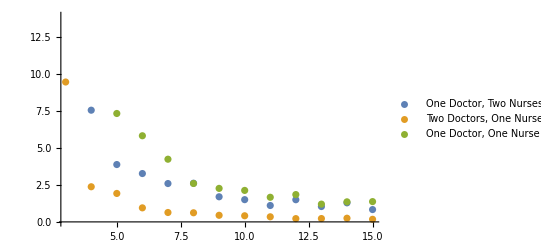

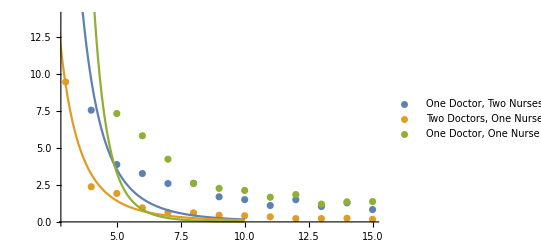

```mathematica
waitPlot = ListPlot[{oneTwoData[[;;,1;;2]],twoOneData[[;;,1;;2]], oneOneData[[;;,1;;2]]}, PlotTheme->"Default", PlotLegends->{"One Doctor, Two Nurses","Two Doctors, One Nurse","One Doctor, One Nurse"}]
fits = {NonlinearModelFit[oneTwoData[[;;,1;;2]],a x^b,{a,b},x],NonlinearModelFit[twoOneData[[;;,1;;2]],a x^b,{a,b},x],NonlinearModelFit[oneOneData[[;;,1;;2]],a x^b, {a,b},x] };
fitPlot=Plot[{fits[[1]][i],fits[[2]][i],fits[[3]][i]},{i,0,10}];
Show[waitPlot,fitPlot]
```